## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Generate global Har translation decay plots

### Reading In Parameters:

```mathematica
AALength=1717;
(* using 1717 AA because that's half of the smFLAG tag and the entire ORF of KDM5B*)
myStartTime=5;
myEndTime=65;
```

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

### Reading In Files

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = FileNames["*ySpotNTime.m",myFolders];
Length@myYellowOnlyFiles
```

22

```mathematica
myWhiteFiles =FileNames["*wSpotNTime.m",myFolders];
Length@myWhiteFiles
```

22

```mathematica
myAllYellowFiles = FileNames["*gSpotNTime.m",myFolders];
Length@myAllYellowFiles
```

22

```mathematica
myPurpleFiles = FileNames["*brSpotNTime.m",myFolders];
Length@myPurpleFiles
```

22

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Import[myYellowOnlyFiles⟦j⟧],{j,1,Length@myYellowOnlyFiles,1}];
```

```mathematica
cellCount = Length@onlyYellow
```

22

```mathematica
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,212},{-118,195},{-58,185},{2,176},{62,183},{122,200},{182,187},{242,188},{302,178},{362,158},{422,164},{482,160},{542,149},{602,136},{662,134},{722,122},{782,121},{842,128},{902,108},{962,106},{1022,107},{1082,97},{1142,108},{1202,84},{1262,91},{1322,91},{1382,84},{1442,86},{1502,86},{1562,76},{1622,72},{1682,73},{1742,78},{1802,67},{1862,58},{1922,59},{1982,66},{2042,57},{2102,52},{2162,50},{2222,54},{2282,46},{2342,55},{2402,52},{2462,42},{2522,50},{2582,36},{2642,32},{2702,42},{2762,33},{2822,34},{2882,39},{2942,34},{3002,30},{3062,32},{3122,28},{3182,28},{3242,33},{3302,28},{3362,26},{3422,29},{3482,25},{3542,32},{3602,36},{3662,21}}

{{-178,212},{-118,195},{-58,185},{2,176},{62,183},{122,200},{182,187},{242,188},{302,178},{362,158},{422,164},{482,160},{542,149},{602,136},{662,134},{722,122},{782,121},{842,128},{902,108},{962,106},{1022,107},{1082,97},{1142,108},{1202,84},{1262,91},{1322,91},{1382,84},{1442,86},{1502,86},{1562,76},{1622,72},{1682,73},{1742,78},{1802,67},{1862,58},{1922,59},{1982,66},{2042,57},{2102,52},{2162,50},{2222,54},{2282,46},{2342,55},{2402,52},{2462,42},{2522,50},{2582,36},{2642,32},{2702,42},{2762,33},{2822,34},{2882,39},{2942,34},{3002,30},{3062,32},{3122,28},{3182,28},{3242,33},{3302,28},{3362,26},{3422,29},{3482,25},{3542,32},{3602,36},{3662,21}}

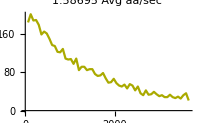
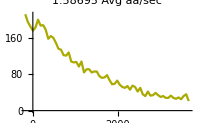
{{1.58695,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
myYelOnlySpotTime = spotTime;
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
spotTime>>analysisFolder<>"_OnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Import[myAllYellowFiles⟦j⟧],{j,1,Length@myAllYellowFiles,1}];
```

```mathematica
cellCount = Length@allYellow
```

22

```mathematica
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,303},{-118,289},{-58,266},{2,251},{62,266},{122,272},{182,279},{242,260},{302,255},{362,234},{422,229},{482,219},{542,211},{602,203},{662,187},{722,188},{782,182},{842,178},{902,161},{962,164},{1022,151},{1082,139},{1142,151},{1202,131},{1262,139},{1322,138},{1382,135},{1442,124},{1502,128},{1562,124},{1622,111},{1682,117},{1742,124},{1802,100},{1862,91},{1922,99},{1982,99},{2042,90},{2102,80},{2162,76},{2222,78},{2282,77},{2342,78},{2402,77},{2462,65},{2522,71},{2582,59},{2642,60},{2702,60},{2762,52},{2822,52},{2882,52},{2942,48},{3002,48},{3062,44},{3122,36},{3182,39},{3242,44},{3302,42},{3362,33},{3422,36},{3482,36},{3542,41},{3602,45},{3662,32}}

{{-178,303},{-118,289},{-58,266},{2,251},{62,266},{122,272},{182,279},{242,260},{302,255},{362,234},{422,229},{482,219},{542,211},{602,203},{662,187},{722,188},{782,182},{842,178},{902,161},{962,164},{1022,151},{1082,139},{1142,151},{1202,131},{1262,139},{1322,138},{1382,135},{1442,124},{1502,128},{1562,124},{1622,111},{1682,117},{1742,124},{1802,100},{1862,91},{1922,99},{1982,99},{2042,90},{2102,80},{2162,76},{2222,78},{2282,77},{2342,78},{2402,77},{2462,65},{2522,71},{2582,59},{2642,60},{2702,60},{2762,52},{2822,52},{2882,52},{2942,48},{3002,48},{3062,44},{3122,36},{3182,39},{3242,44},{3302,42},{3362,33},{3422,36},{3482,36},{3542,41},{3602,45},{3662,32}}

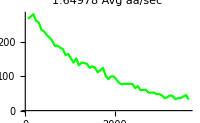
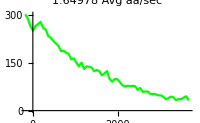
{{1.64978,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
yelAllTime = spotTime;
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",yelAllTimePlot];
yelAllTimePlot>>analysisFolder<>"_yAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Import[myWhiteFiles⟦j⟧],{j,1,Length@myWhiteFiles,1}];
```

```mathematica
cellCount = Length@white
```

22

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
whiteSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,91},{-118,94},{-58,81},{2,75},{62,83},{122,72},{182,92},{242,72},{302,77},{362,76},{422,65},{482,59},{542,62},{602,67},{662,53},{722,66},{782,61},{842,50},{902,53},{962,58},{1022,44},{1082,42},{1142,43},{1202,47},{1262,48},{1322,47},{1382,51},{1442,38},{1502,42},{1562,48},{1622,39},{1682,44},{1742,46},{1802,33},{1862,33},{1922,40},{1982,33},{2042,33},{2102,28},{2162,26},{2222,24},{2282,31},{2342,23},{2402,25},{2462,23},{2522,21},{2582,23},{2642,28},{2702,18},{2762,19},{2822,18},{2882,13},{2942,14},{3002,18},{3062,12},{3122,8},{3182,11},{3242,11},{3302,14},{3362,7},{3422,7},{3482,11},{3542,9},{3602,9},{3662,11}}

{{-178,91},{-118,94},{-58,81},{2,75},{62,83},{122,72},{182,92},{242,72},{302,77},{362,76},{422,65},{482,59},{542,62},{602,67},{662,53},{722,66},{782,61},{842,50},{902,53},{962,58},{1022,44},{1082,42},{1142,43},{1202,47},{1262,48},{1322,47},{1382,51},{1442,38},{1502,42},{1562,48},{1622,39},{1682,44},{1742,46},{1802,33},{1862,33},{1922,40},{1982,33},{2042,33},{2102,28},{2162,26},{2222,24},{2282,31},{2342,23},{2402,25},{2462,23},{2522,21},{2582,23},{2642,28},{2702,18},{2762,19},{2822,18},{2882,13},{2942,14},{3002,18},{3062,12},{3122,8},{3182,11},{3242,11},{3302,14},{3362,7},{3422,7},{3482,11},{3542,9},{3602,9},{3662,11}}

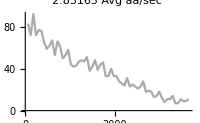
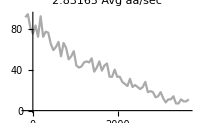
{{2.83165,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
whiteTime = spotTime
```

{{-178,91},{-118,94},{-58,81},{2,75},{62,83},{122,72},{182,92},{242,72},{302,77},{362,76},{422,65},{482,59},{542,62},{602,67},{662,53},{722,66},{782,61},{842,50},{902,53},{962,58},{1022,44},{1082,42},{1142,43},{1202,47},{1262,48},{1322,47},{1382,51},{1442,38},{1502,42},{1562,48},{1622,39},{1682,44},{1742,46},{1802,33},{1862,33},{1922,40},{1982,33},{2042,33},{2102,28},{2162,26},{2222,24},{2282,31},{2342,23},{2402,25},{2462,23},{2522,21},{2582,23},{2642,28},{2702,18},{2762,19},{2822,18},{2882,13},{2942,14},{3002,18},{3062,12},{3122,8},{3182,11},{3242,11},{3302,14},{3362,7},{3422,7},{3482,11},{3542,9},{3602,9},{3662,11}}

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",whiteTimePlot];
whiteTimePlot>>analysisFolder<>"_wGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Import[myPurpleFiles⟦j⟧],{j,1,Length@myPurpleFiles,1}];
```

```mathematica
cellCount = Length@purple
```

22

```mathematica
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
times = Total[Transpose[purple],{2}]//#[[All,1]]/cellCount&;
purpleSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,337},{-118,337},{-58,305},{2,303},{62,328},{122,320},{182,322},{242,318},{302,312},{362,308},{422,298},{482,315},{542,299},{602,315},{662,318},{722,318},{782,311},{842,300},{902,315},{962,296},{1022,290},{1082,297},{1142,286},{1202,294},{1262,294},{1322,294},{1382,309},{1442,295},{1502,320},{1562,301},{1622,293},{1682,286},{1742,291},{1802,274},{1862,268},{1922,264},{1982,287},{2042,280},{2102,279},{2162,280},{2222,251},{2282,303},{2342,286},{2402,276},{2462,253},{2522,290},{2582,271},{2642,283},{2702,272},{2762,270},{2822,274},{2882,267},{2942,257},{3002,279},{3062,283},{3122,278},{3182,269},{3242,256},{3302,252},{3362,260},{3422,285},{3482,275},{3542,259},{3602,255},{3662,270}}

{{-178,337},{-118,337},{-58,305},{2,303},{62,328},{122,320},{182,322},{242,318},{302,312},{362,308},{422,298},{482,315},{542,299},{602,315},{662,318},{722,318},{782,311},{842,300},{902,315},{962,296},{1022,290},{1082,297},{1142,286},{1202,294},{1262,294},{1322,294},{1382,309},{1442,295},{1502,320},{1562,301},{1622,293},{1682,286},{1742,291},{1802,274},{1862,268},{1922,264},{1982,287},{2042,280},{2102,279},{2162,280},{2222,251},{2282,303},{2342,286},{2402,276},{2462,253},{2522,290},{2582,271},{2642,283},{2702,272},{2762,270},{2822,274},{2882,267},{2942,257},{3002,279},{3062,283},{3122,278},{3182,269},{3242,256},{3302,252},{3362,260},{3422,285},{3482,275},{3542,259},{3602,255},{3662,270}}

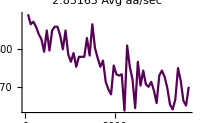
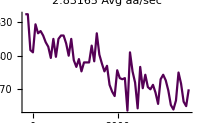
{{2.83165,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
purpleTime = spotTime
```

{{-178,337},{-118,337},{-58,305},{2,303},{62,328},{122,320},{182,322},{242,318},{302,312},{362,308},{422,298},{482,315},{542,299},{602,315},{662,318},{722,318},{782,311},{842,300},{902,315},{962,296},{1022,290},{1082,297},{1142,286},{1202,294},{1262,294},{1322,294},{1382,309},{1442,295},{1502,320},{1562,301},{1622,293},{1682,286},{1742,291},{1802,274},{1862,268},{1922,264},{1982,287},{2042,280},{2102,279},{2162,280},{2222,251},{2282,303},{2342,286},{2402,276},{2462,253},{2522,290},{2582,271},{2642,283},{2702,272},{2762,270},{2822,274},{2882,267},{2942,257},{3002,279},{3062,283},{3122,278},{3182,269},{3242,256},{3302,252},{3362,260},{3422,285},{3482,275},{3542,259},{3602,255},{3662,270}}

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",purpleTimePlot];
purpleSpotWeights>>analysisFolder<>"_pGlobalTime.m"
```

### View it all...

```mathematica
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot
}]
```

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = Length@onlyYellowSpots  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

6

30

### BS for Only Yellow Spots:

```mathematica
onlyYellow//Dimensions
```

{22,65,2}

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}]}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

-Graphics-

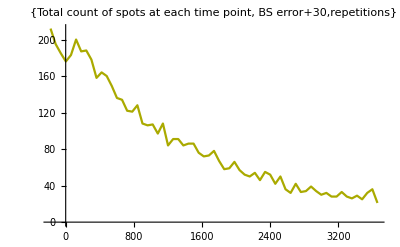

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for All Yellow Spots:

```mathematica
allYellow//Dimensions
```

{6,65,2}

```mathematica
allYellowSpots = allYellow[[All,All,2]];
allYellowSpots
```

{{8,10,11,11,9,10,9,10,14,9,7,6,9,8,8,8,6,6,6,8,7,7,4,7,3,6,7,7,7,10,8,7,7,8,7,7,8,9,7,3,8,6,6,4,6,4,4,2,5,4,4,7,6,5,3,4,3,6,6,5,3,4,3,4,4},{25,25,21,25,23,12,21,22,17,25,20,22,23,20,13,24,19,18,20,16,17,22,22,13,19,20,17,14,21,17,18,12,19,17,12,15,13,8,7,11,8,9,12,8,11,12,10,12,12,8,7,5,5,10,9,3,4,4,9,4,1,3,3,7,3},{10,10,5,3,12,9,7,8,7,7,4,6,7,6,4,7,6,8,4,5,4,1,4,7,8,4,3,2,4,2,1,5,3,1,1,1,3,0,0,1,1,2,2,3,2,2,3,4,0,2,1,5,0,2,2,0,2,2,1,1,2,0,0,4,0},{7,5,10,10,9,7,8,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{33,31,24,22,18,20,26,18,25,16,13,9,11,12,6,9,12,9,9,8,8,8,9,5,13,9,12,9,8,8,4,6,8,7,7,5,8,9,8,7,8,5,3,6,4,10,6,6,2,5,3,5,5,7,4,4,4,3,2,4,3,2,3,3,5},{26,22,20,20,21,21,15,23,17,14,18,14,14,15,18,12,18,13,17,11,8,9,10,10,11,11,12,11,8,11,6,9,7,9,4,9,7,8,9,6,11,10,5,5,6,2,6,4,6,6,4,6,5,1,5,0,3,2,1,1,2,2,3,3,2}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[allYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelAllSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{3.94448,4.19161,2.84958,3.08871,2.39505,1.96165,2.67706,3.554,2.15684,2.22651,2.79262,2.07918,1.81632,1.92231,2.11291,2.33002,2.18072,1.74059,2.5692,1.84765,1.90557,2.35283,2.5836,1.33978,2.55004,1.97966,2.38479,1.58356,2.37229,1.88104,1.67432,1.25105,2.07186,2.14757,1.42847,1.72151,1.47661,1.09679,1.05816,1.41715,1.36804,1.11962,1.08956,0.793271,1.30746,2.04299,1.00797,1.40312,1.86916,1.15547,0.778954,0.653241,1.07344,1.32464,1.05929,0.596097,0.367458,0.488174,1.2313,0.665132,0.289283,0.40337,0.394769,1.1944,0.668604}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{21.1667,18.,18.5,23.6667,20.8333,17.,23.6667,17.6667,22.5,20.3333,23.,16.1667,23.3333,18.5,14.,11.8333,25.,17.6667,18.1667,10.8333,20.8333,16.8333,20.,18.5,21.8333,15.1667,28.,18.6667,25.,15.8333}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{yelAllTime ,errorBS}];
```

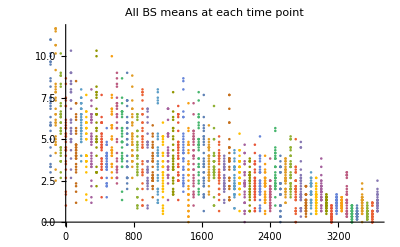

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

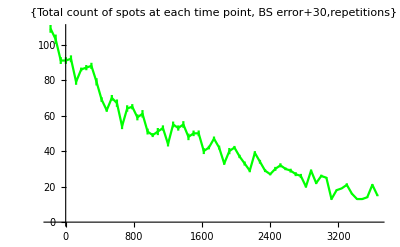

```mathematica
ErrorListPlot[b,PlotStyle->{Green}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for White Spots:

```mathematica
white//Dimensions
```

{6,65,2}

```mathematica
white = white[[All,All,2]];
white
```

{{2,2,4,5,4,3,4,2,3,2,3,3,5,2,3,4,1,1,1,3,3,2,1,2,1,2,2,2,2,5,4,5,4,2,4,6,2,6,0,2,1,1,2,2,4,0,1,1,1,1,2,1,2,1,2,0,2,2,1,0,1,2,1,1,3},{11,10,9,10,8,5,11,10,11,13,8,8,12,10,7,12,8,8,12,9,8,13,11,10,11,12,13,11,12,10,11,7,10,7,5,10,5,6,3,7,4,5,6,5,7,8,6,9,7,7,3,2,2,5,2,2,2,1,5,2,0,3,2,3,1},{7,9,3,2,7,5,6,6,2,5,2,1,5,4,3,4,5,6,3,4,3,1,2,3,1,3,2,0,1,1,1,4,0,0,1,0,0,0,0,0,0,0,0,1,1,0,2,2,0,1,0,2,0,2,1,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,6,5,2,4,1,5,2,3,3,4,1,1,3,1,2,5,1,1,1,2,2,1,1,5,3,5,0,3,1,1,1,2,1,3,1,3,2,4,2,2,3,1,1,2,2,4,1,0,0,1,1,1,2,0,1,0,1,1,0,0,0,0,0,2},{17,15,13,10,14,14,10,8,10,8,11,7,7,13,12,8,13,9,10,8,5,7,5,9,8,6,6,6,4,8,3,4,5,7,3,5,5,2,7,4,7,6,4,1,3,2,3,4,4,4,1,5,4,1,3,0,2,1,1,0,1,2,1,0,1}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[white[[All,i]]],sampleSize],repetitions ],{i,1,Length@whiteSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{2.88456,2.07549,1.9379,1.65768,1.95515,2.12403,1.34316,1.23611,1.15178,1.58155,1.56629,1.02711,1.31332,1.6798,1.61432,1.46762,1.7698,1.45394,2.12012,1.44137,0.97176,1.89734,1.79288,1.81279,1.63627,2.30749,1.93896,1.47634,1.74633,1.721,1.20403,1.00801,1.27577,1.05294,0.603206,1.62578,0.766558,1.24599,1.13643,0.895016,0.891996,1.1994,0.811181,0.50729,0.757255,1.14966,0.892068,1.17362,0.982364,1.02715,0.513204,0.577599,0.500829,0.591662,0.399113,0.304343,0.247594,0.233593,0.470082,0.434025,0.197688,0.499201,0.216202,0.436995,0.456296}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{5.83333,3.83333,13.,9.16667,5.,3.83333,11.,6.,4.5,7.5,8.5,10.6667,10.6667,3.66667,7.16667,10.6667,8.66667,5.83333,2.83333,10.6667,3.5,4.,3.66667,8.,5.66667,6.16667,9.16667,4.,3.83333,9.}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{whiteTime ,errorBS}];
```

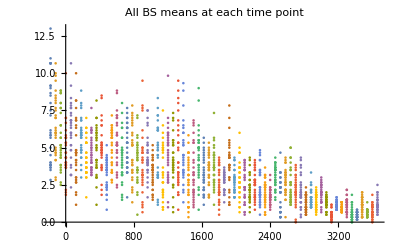

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

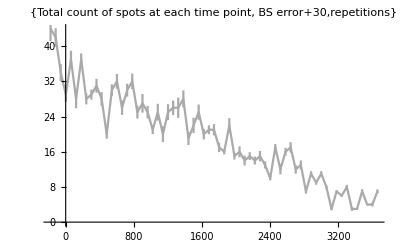

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[White]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for Purple Spots:

```mathematica
purple//Dimensions
```

{6,65,2}

```mathematica
purple = purple[[All,All,2]]
```

{{9,10,11,11,11,6,8,7,8,11,7,7,12,7,8,8,5,10,6,9,7,7,6,7,9,6,9,7,12,7,12,12,8,9,8,11,8,7,9,6,6,8,7,10,6,6,7,7,8,8,10,8,9,7,8,9,9,7,7,10,11,6,8,5,10},{44,37,38,34,36,49,41,42,47,38,33,43,41,41,48,41,48,45,49,46,31,45,43,40,41,46,44,49,46,45,46,42,45,37,38,33,41,55,52,44,44,55,50,44,40,49,43,57,48,38,47,42,47,53,40,51,53,39,40,40,44,52,42,46,47},{37,44,26,33,45,40,43,49,37,45,45,51,42,46,43,37,44,44,50,46,48,48,48,49,51,41,46,43,56,52,50,42,40,41,40,40,42,41,37,44,38,39,40,45,47,40,45,46,42,46,46,44,43,47,49,44,41,41,43,40,52,45,48,40,46},{0,0,0,1,2,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0},{21,20,18,12,10,7,17,15,14,20,17,18,12,13,18,16,23,15,16,9,14,13,10,15,16,19,18,12,13,11,11,9,13,10,13,10,15,13,15,18,14,19,14,21,15,20,18,11,12,12,14,14,8,20,14,9,12,13,16,16,13,13,13,14,17},{40,41,35,39,38,39,34,36,34,31,32,35,39,38,40,36,35,37,36,38,36,32,31,38,30,39,36,34,39,39,36,34,38,37,38,37,35,32,37,37,32,39,39,34,36,40,36,36,38,37,32,37,36,37,35,34,35,32,30,32,37,37,32,36,32}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[purple[[All,i]]],sampleSize],repetitions ],{i,1,Length@purpleSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{8.77547,6.73206,6.96068,5.99986,6.36618,9.31016,6.27,7.11209,7.48464,6.26869,6.51578,9.47541,6.66735,9.91946,7.63524,6.47656,6.75598,7.78168,6.72761,8.33393,8.55916,7.50437,6.23108,7.05108,7.5817,6.59023,7.43505,7.35466,8.53623,7.95277,8.52938,6.21393,6.55298,6.75388,5.78636,6.58592,6.66694,7.56855,6.10589,7.57766,7.81961,7.11823,9.31577,5.55249,7.06082,6.8129,6.98506,5.7904,8.08831,6.53138,8.21009,8.16866,7.04983,9.51238,7.62174,7.39503,7.6232,6.66415,5.1896,6.68079,6.75923,6.82739,7.48422,6.57152,6.0066}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{17.8333,29.1667,5.,30.8333,35.3333,27.3333,19.8333,16.5,34.5,31.1667,40.8333,33.6667,17.,30.5,38.3333,18.8333,20.5,20.,28.6667,22.3333,33.,31.5,20.1667,33.3333,15.1667,13.8333,18.,13.3333,19.3333,17.1667}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{purpleTime ,errorBS}];
```

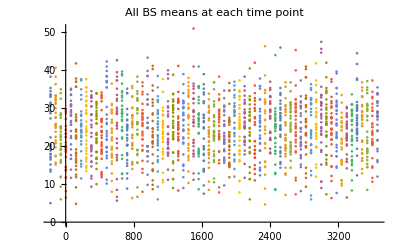

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

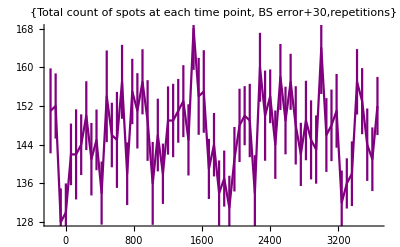

```mathematica
ErrorListPlot[b,PlotStyle->{Purple}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```